```mathematica
SetDirectory["G:\\johnny\\matlab\\jlhbpe\\2016_10_projects"]
```

G:\johnny\matlab\jlhbpe\2016_10_projects

```mathematica
SetDirectory["~/g/johnny/matlab/jlhbpe/2016_10_projects"]
```

/media/jotelha/storage/windows/Users/jotelha/Google Docs/johnny/matlab/jlhbpe/2016_10_projects

## Import data

```mathematica
adMass1mA=Import["zhang2015control_adsorption_mass_fig4_0_1mA.txt","Table"][[3;;]];
```

```mathematica
adMass2mA=Import["zhang2015control_adsorption_mass_fig4_0_2mA.txt","Table"][[3;;]];
```

```mathematica
adMass4mA=Import["zhang2015control_adsorption_mass_fig4_0_4mA.txt","Table"][[3;;]];
```

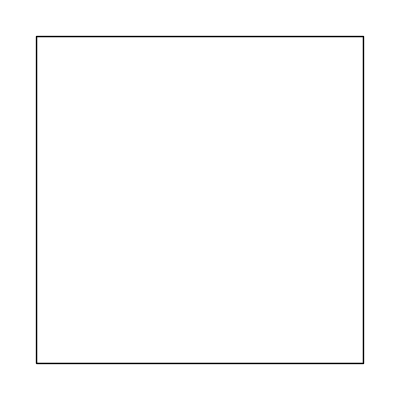

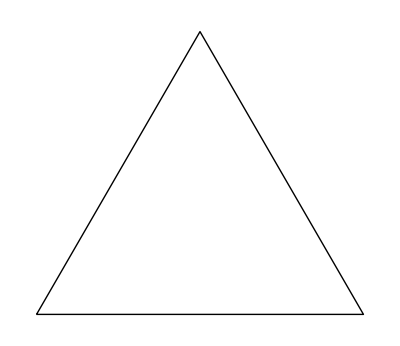

```mathematica
{m1,m2,m3}=Graphics/@{Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],Circle[{0,0},1],Line[{{-0.5,-0.5},{0.5,-0.5},{0,(Sqrt[3]-1)/2},{-0.5,-0.5}}]}
```

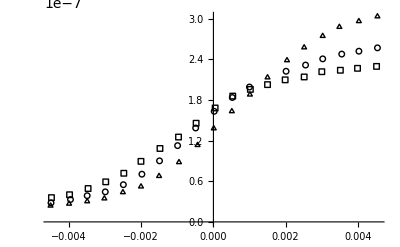

```mathematica
trueMassPlot=ListPlot[{adMass1mA,adMass2mA,adMass4mA},PlotStyle->Black,PlotMarkers->{{□,Medium},{○,Medium},{△,Medium}}]
```

```mathematica
plegend=PointLegend[Table[Black,{3}],{"1 mA","2 mA","4 mA"},LegendMarkerSize->{10,10},LegendMarkers->{{m1,1},{m2,1},{m3,1}},LabelStyle->{GrayLevel[0.0],12}]
```

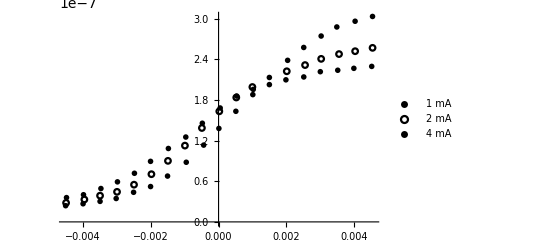

```mathematica
trueMassPlotWithLegend=ListPlot[{adMass1mA,adMass2mA,adMass4mA},PlotStyle->Black,PlotMarkers->Table[{s,0.03},{s,{m1,m2,m3}}],PlotLegends->Placed[plegend,{0.15,0.75}]]
```

```mathematica
dat1mA=Import["zhang2015control_surface_data_0_1mA.txt","Data"][[2;;]];
```

```mathematica
dat2mA=Import["zhang2015control_surface_data_0_2mA.txt","Data"][[2;;]];
```

```mathematica
dat4mA=Import["zhang2015control_surface_data_0_4mA.txt","Data"][[2;;]];
```

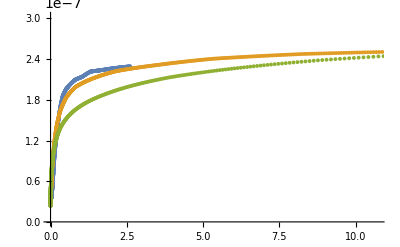

```mathematica
refPlot=ListPlot[{Table[{dat1mA[[n]][[2]],dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}],
Table[{dat2mA[[n]][[2]],dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}],
Table[{dat4mA[[n]][[2]],dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}]}]
```

```mathematica
refIsotherm1mA=Table[{dat1mA[[n]][[2]],dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}];
```

```mathematica
refIsotherm2mA=Table[{dat2mA[[n]][[2]],dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}];
```

```mathematica
refIsotherm4mA=Table[{dat4mA[[n]][[2]],dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}];
```

```mathematica
refReverseIsotherm1mA=Table[{dat1mA[[n]][[3]],dat1mA[[n]][[2]]},{n,1,Length[dat1mA]}];
```

```mathematica
refReverseIsotherm2mA=Table[{dat2mA[[n]][[3]],dat2mA[[n]][[2]]},{n,1,Length[dat2mA]}];
```

```mathematica
refReverseIsotherm4mA=Table[{dat4mA[[n]][[3]],dat4mA[[n]][[2]]},{n,1,Length[dat4mA]}];
```

```mathematica
refReverseLogIsotherm1mA=Table[{dat1mA[[n]][[3]],Log[dat1mA[[n]][[2]]]},{n,1,Length[dat1mA]}];
```

```mathematica
refReverseLogIsotherm2mA=Table[{dat2mA[[n]][[3]],Log[dat2mA[[n]][[2]]]},{n,1,Length[dat2mA]}];
```

```mathematica
refReverseLogIsotherm4mA=Table[{dat4mA[[n]][[3]],Log[dat4mA[[n]][[2]]]},{n,1,Length[dat4mA]}];
```

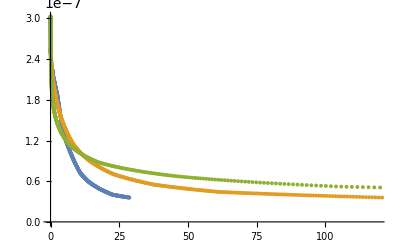

```mathematica
ListPlot[{Table[{1/dat1mA[[n]][[2]],dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}],
Table[{1/dat2mA[[n]][[2]],dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}],
Table[{1/dat4mA[[n]][[2]],dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}]}]
```

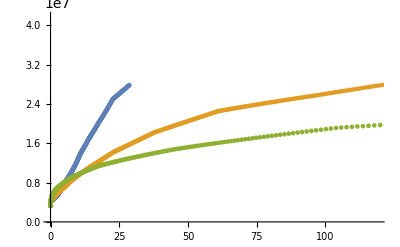

```mathematica
ListPlot[{Table[{1/dat1mA[[n]][[2]],1/dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}],
Table[{1/dat2mA[[n]][[2]],1/dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}],
Table[{1/dat4mA[[n]][[2]],1/dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}]}]
```

## Reference Plots :

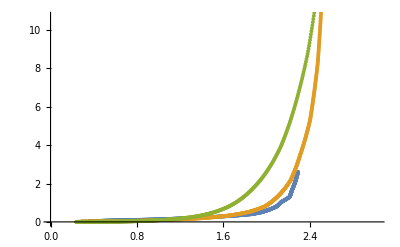

```mathematica
refReverseIsothermPlot=ListPlot[{refReverseIsotherm1mA,refReverseIsotherm2mA,refReverseIsotherm4mA}]
```

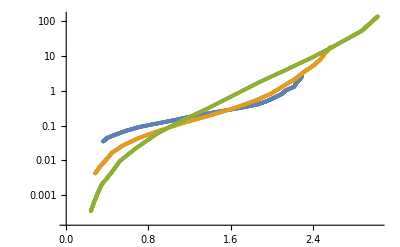

```mathematica
refReverseIsothermLogPlot=ListLogPlot[{refReverseIsotherm1mA,refReverseIsotherm2mA,refReverseIsotherm4mA}]
```

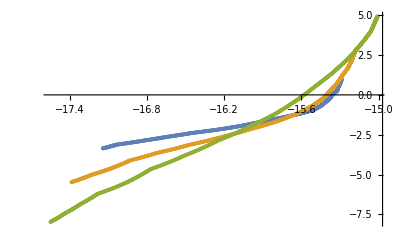

```mathematica
refReverseIsothermLogLogPlot=ListPlot[Log[{refReverseIsotherm1mA,refReverseIsotherm2mA,refReverseIsotherm4mA}]]
```

## Frumkin and Bockris Log fits

```mathematica
First[refReverseLogIsotherm4mA][[1]]
```

2.39057×10^-8

```mathematica
First[refReverseLogIsotherm2mA][[1]]
```

2.81088×10^-8

```mathematica
First[refReverseLogIsotherm1mA][[1]]
```

3.59078×10^-8

```mathematica
Last[refReverseLogIsotherm4mA][[1]]
```

3.02975×10^-7

```mathematica
Last[refReverseLogIsotherm2mA][[1]]
```

2.56801×10^-7

```mathematica
Last[refReverseLogIsotherm1mA][[1]]
```

2.29391×10^-7

```mathematica
refReverseLogIsotherm4mANormCorrected = Table[{(refReverseLogIsotherm4mA[[n,1]]-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]),refReverseLogIsotherm4mA[[n,2]]},{n,1,Length[refReverseLogIsotherm4mA]}];
```

```mathematica
refReverseLogIsotherm2mANormCorrected = Table[{(refReverseLogIsotherm2mA[[n,1]]-First[refReverseLogIsotherm2mA][[1]])/(Last[refReverseLogIsotherm2mA][[1]]-First[refReverseLogIsotherm2mA][[1]]),refReverseLogIsotherm2mA[[n,2]]},{n,1,Length[refReverseLogIsotherm2mA]}];
```

```mathematica
refReverseLogIsotherm1mANormCorrected = Table[{(refReverseLogIsotherm1mA[[n,1]]-First[refReverseLogIsotherm1mA][[1]])/(Last[refReverseLogIsotherm1mA][[1]]-First[refReverseLogIsotherm1mA][[1]]),refReverseLogIsotherm1mA[[n,2]]},{n,1,Length[refReverseLogIsotherm1mA]}];
```

```mathematica
linearizedReverseIsotherm4mA=Table[{refReverseLogIsotherm4mANormCorrected[[n,1]],refReverseLogIsotherm4mANormCorrected[[n,2]]-Log[refReverseLogIsotherm4mANormCorrected[[n,1]]]+Log[1-refReverseLogIsotherm4mANormCorrected[[n,1]]]},{n,1,Length[refReverseLogIsotherm4mA]}];
```

```mathematica
linearizedReverseIsotherm2mA=Table[{refReverseLogIsotherm2mANormCorrected[[n,1]],refReverseLogIsotherm2mANormCorrected[[n,2]]-Log[refReverseLogIsotherm2mANormCorrected[[n,1]]]+Log[1-refReverseLogIsotherm2mANormCorrected[[n,1]]]},{n,1,Length[refReverseLogIsotherm2mA]}];
linearizedReverseIsotherm1mA=Table[{refReverseLogIsotherm1mANormCorrected[[n,1]],refReverseLogIsotherm1mANormCorrected[[n,2]]-Log[refReverseLogIsotherm1mANormCorrected[[n,1]]]+Log[1-refReverseLogIsotherm1mANormCorrected[[n,1]]]},{n,1,Length[refReverseLogIsotherm1mA]}];
```

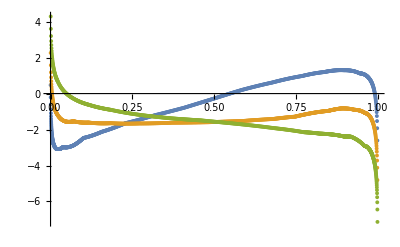

```mathematica
ListPlot[{linearizedReverseIsotherm4mA,linearizedReverseIsotherm2mA,linearizedReverseIsotherm1mA}]
```

```mathematica
frumkinFit4mA=Fit[linearizedReverseIsotherm4mA[[2;;(Length[linearizedReverseIsotherm4mA]-1)]],
{1,th},th]
```

-2.7475+4.26509 th

```mathematica
frumkinFit2mA=Fit[linearizedReverseIsotherm2mA[[2;;(Length[linearizedReverseIsotherm2mA]-1)]],
{1,th},th]
```

-1.43582+0.191123 th

```mathematica
frumkinFit1mA=Fit[linearizedReverseIsotherm1mA[[2;;(Length[linearizedReverseIsotherm1mA]-1)]],
{1,th},th]
```

0.227643-3.37191 th

```mathematica
frumkinIsotherm1mANSolve[c_]:=Quiet[NSolve[frumkinFit1mA==Log[c]-Log[th]+Log[1-th],th,Reals]][[1]]
```

```mathematica
frumkinIsotherm2mANSolve[c_]:=Quiet[NSolve[frumkinFit2mA==Log[c]-Log[th]+Log[1-th],th,Reals]][[1]]
```

```mathematica
frumkinIsotherm4mANSolve[c_]:=Quiet[NSolve[frumkinFit4mA==Log[c]-Log[th]+Log[1-th],th,Reals]][[1]]
```

```mathematica
fitDat1mA = Table[{dat1mA[[n,1]],N[th/.frumkinIsotherm1mANSolve[dat1mA[[n,2]]]]},{n,1,Length[dat1mA]}];
```

```mathematica
fitDat2mA = Table[{dat2mA[[n,1]],N[th/.frumkinIsotherm2mANSolve[dat2mA[[n,2]]]]},{n,1,Length[dat2mA]}];
```

```mathematica
fitDat4mA = Table[{dat4mA[[n,1]],N[th/.frumkinIsotherm4mANSolve[dat4mA[[n,2]]]]},{n,1,Length[dat4mA]}];
```

```mathematica
massPredictionDat1mA = Table[{dat1mA[[n,1]],
N[th/.frumkinIsotherm1mANSolve[dat1mA[[n,2]]]]
*(Last[refReverseLogIsotherm1mA][[1]]-First[refReverseLogIsotherm1mA][[1]])+First[refReverseLogIsotherm1mA][[1]]},{n,1,Length[dat1mA]}];
```

```mathematica
massPredictionDat2mA = Table[{dat2mA[[n,1]],
N[th/.frumkinIsotherm2mANSolve[dat2mA[[n,2]]]]
*(Last[refReverseLogIsotherm2mA][[1]]-First[refReverseLogIsotherm2mA][[1]])+First[refReverseLogIsotherm2mA][[1]]},{n,1,Length[dat2mA]}];
```

```mathematica
massPredictionDat4mA = Table[{dat4mA[[n,1]],
N[th/.frumkinIsotherm4mANSolve[dat4mA[[n,2]]]]
*(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])+First[refReverseLogIsotherm4mA][[1]]},{n,1,Length[dat4mA]}];
```

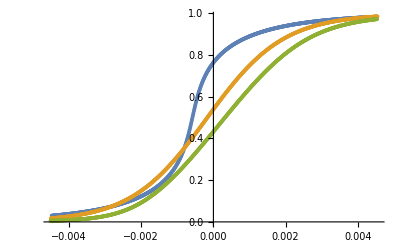

```mathematica
ListPlot[{fitDat1mA,fitDat2mA,fitDat4mA}]
```

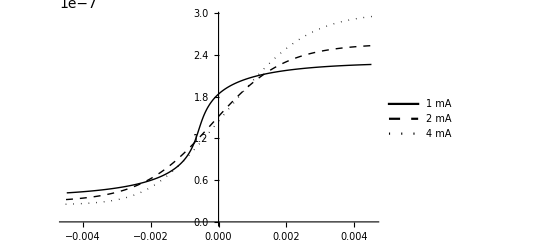

```mathematica
massPredictionDatPlot=ListLinePlot[{massPredictionDat1mA,massPredictionDat2mA,massPredictionDat4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[{"1 mA","2 mA","4 mA"},{0.75,0.25}]]
```

```mathematica
modifiedFrumkinFitInfo4mA=LinearModelFit[refReverseLogIsotherm4mANormCorrected[[2;;(Length[refReverseLogIsotherm4mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

FittedModel[-4.3502+7.40358 th+0.555019 (-Log[1-th]+Log[th])]

```mathematica
modifiedFrumkinFit4mA=Fit[refReverseLogIsotherm4mANormCorrected[[2;;(Length[refReverseLogIsotherm4mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

-4.3502+7.40358 th+0.555019 (-Log[1-th]+Log[th])

```mathematica
modifiedFrumkinFitInfo4mA=LinearModelFit[refReverseLogIsotherm4mANormCorrected[[2;;(Length[refReverseLogIsotherm4mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

FittedModel[-4.3502+7.40358 th+0.555019 (-Log[1-th]+Log[th])]

```mathematica
modifiedFrumkinFitInfo4mA["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
th | 1 | 13168.8 | 13168.8 | 79690.2 | 1.8837764078×10^-817
-Log[1-th]+Log[th] | 1 | 160.736 | 160.736 | 972.685 | 2.56323×10^-141
Error | 818 | 135.175 | 0.16525 |  | 
Total | 820 | 13464.7 |  |  |

```mathematica
modifiedFrumkinFitInfo4mA["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | -4.3502 | 0.0680447 | {-4.48377,-4.21664}
th | 7.40358 | 0.131765 | {7.14495,7.66222}
-Log[1-th]+Log[th] | 0.555019 | 0.017796 | {0.520088,0.58995}

```mathematica
a04mA=modifiedFrumkinFit4mA[[1]]
```

-4.3502

```mathematica
a14mA=modifiedFrumkinFit4mA[[2]][[1]]
```

7.40358

```mathematica
a24mA=modifiedFrumkinFit4mA[[3]][[1]]
```

0.555019

```mathematica
A4mA=-2*a24mA/a14mA
```

-0.149932

```mathematica
beta4mA=Exp[-a04mA/a24mA]
```

2534.98

```mathematica
gamma4mA=1/a24mA
```

1.80174

```mathematica
modifiedFrumkinFitInfo4mA["ParameterConfidenceIntervals"]
```

{{-4.48377,-4.21664},{7.14495,7.66222},{0.520088,0.58995}}

```mathematica
modifiedFrumkinFit2mA=Fit[refReverseLogIsotherm2mANormCorrected[[2;;(Length[refReverseLogIsotherm2mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

-3.42162+4.10408 th+0.419436 (-Log[1-th]+Log[th])

```mathematica
modifiedFrumkinFitInfo2mA=LinearModelFit[refReverseLogIsotherm2mANormCorrected[[2;;(Length[refReverseLogIsotherm2mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

FittedModel[-3.42162+4.10408 th+0.419436 (-Log[1-th]+Log[th])]

```mathematica
modifiedFrumkinFitInfo2mA["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | -3.42162 | 0.0372005 | {-3.49464,-3.3486}
th | 4.10408 | 0.0716434 | {3.96345,4.24471}
-Log[1-th]+Log[th] | 0.419436 | 0.0101799 | {0.399454,0.439418}

```mathematica
a02mA=modifiedFrumkinFit2mA[[1]]
```

-3.42162

```mathematica
a12mA=modifiedFrumkinFit2mA[[2]][[1]]
```

4.10408

```mathematica
a22mA=modifiedFrumkinFit2mA[[3]][[1]]
```

0.419436

```mathematica
A2mA=-2*a22mA/a12mA
```

-0.204399

```mathematica
beta2mA=Exp[-a02mA/a22mA]
```

3490.07

```mathematica
gamma2mA=1/a22mA
```

2.38416

```mathematica
modifiedFrumkinFit1mA=Fit[refReverseLogIsotherm1mANormCorrected[[2;;(Length[refReverseLogIsotherm1mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

-2.34523+1.77185 th+0.252778 (-Log[1-th]+Log[th])

```mathematica
modifiedFrumkinFitInfo1mA=LinearModelFit[refReverseLogIsotherm1mANormCorrected[[2;;(Length[refReverseLogIsotherm1mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

FittedModel[-2.34523+1.77185 th+0.252778 (-Log[1-th]+Log[th])]

```mathematica
modifiedFrumkinFitInfo1mA["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | -2.34523 | 0.0275495 | {-2.3993,-2.29115}
th | 1.77185 | 0.053076 | {1.66766,1.87603}
-Log[1-th]+Log[th] | 0.252778 | 0.00734617 | {0.238358,0.267198}

```mathematica
a01mA=modifiedFrumkinFit1mA[[1]]
```

-2.34523

```mathematica
a11mA=modifiedFrumkinFit1mA[[2]][[1]]
```

1.77185

```mathematica
a21mA=modifiedFrumkinFit1mA[[3]][[1]]
```

0.252778

```mathematica
A1mA=-2*a21mA/a11mA
```

-0.285328

```mathematica
beta1mA=Exp[-a01mA/a21mA]
```

10697.9

```mathematica
gamma4mA=1/a21mA
```

3.95604

```mathematica
N[Quantity[1,"BoltzmannConstant"]]
```

1.

```mathematica
UnitConvert[UnitConvert[Quantity["MolarGasConstant"]],"Kelvins Moles/Joules"]
```

Quantity::compat: "Kilograms"\ "Meters"^2/"Kelvins"\ "Moles"\ "Seconds"^2 and "Kelvins"\ "Moles"/"Joules" are incompatible units

$Failed

```mathematica
UnitConvert[Quantity[1,"Joule"]]
```

1

```mathematica
Log[beta1mA]
```

9.27781

```mathematica
Log[beta2mA]
```

8.15768

```mathematica
Log[beta4mA]
```

7.83794

```mathematica
gibbs1mA=N[-UnitConvert[Quantity["MolarGasConstant"]]*Quantity[298.15,"Kelvins"]*Log[beta1mA]]
```

-22999.3

```mathematica
gibbs2mA=N[-UnitConvert[Quantity["MolarGasConstant"]]*Quantity[298.15,"Kelvins"]*Log[beta2mA]]
```

-20222.5

```mathematica
gibbs4mA=N[-UnitConvert[Quantity["MolarGasConstant"]]*Quantity[298.15,"Kelvins"]*Log[beta4mA]]
```

-19429.9

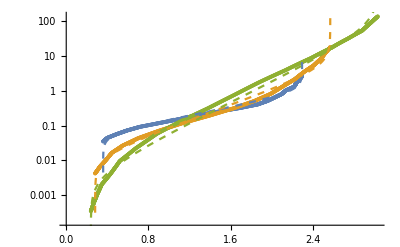

```mathematica
Show[refReverseIsothermLogPlot,Plot[{modifiedFrumkinFit1mA/.th->((m-First[refReverseLogIsotherm1mA][[1]])/(Last[refReverseLogIsotherm1mA][[1]]-First[refReverseLogIsotherm1mA][[1]])),
modifiedFrumkinFit2mA/.th->((m-First[refReverseLogIsotherm2mA][[1]])/(Last[refReverseLogIsotherm2mA][[1]]-First[refReverseLogIsotherm2mA][[1]])),
modifiedFrumkinFit4mA/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]))},
{m,0,Last[refReverseLogIsotherm4mA][[1]]},PlotStyle->Dashed]]
```

```mathematica
modifiedFrumkinFit4mAAbsolute=Fit[refReverseLogIsotherm4mANormCorrectedAbsolute[[2;;(Length[refReverseLogIsotherm4mANormCorrectedAbsolute]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

Part::take: Cannot take positions 2 through -1 in refReverseLogIsotherm4mANormCorrectedAbsolute.

Fit::fitd: First argument refReverseLogIsotherm4mANormCorrectedAbsolute ⟦ 2 ;; -1 ⟧ in Fit is not a list or a rectangular array.

Fit[refReverseLogIsotherm4mANormCorrectedAbsolute⟦2;;-1⟧,{1,th,-Log[1-th]+Log[th]},th]

```mathematica
modifiedFrumkinFit2mAAbsolute=Fit[refReverseLogIsotherm2mANormCorrectedAbsolute,{1,
th,
Log[th]-Log[1-th]},th]
```

Fit::fitd: First argument refReverseLogIsotherm2mANormCorrectedAbsolute in Fit is not a list or a rectangular array.

Fit[refReverseLogIsotherm2mANormCorrectedAbsolute,{1,th,-Log[1-th]+Log[th]},th]

```mathematica
modifiedFrumkinFit1mAAbsolute=Fit[refReverseLogIsotherm1mANormCorrectedAbsolute,{1,
th,
Log[th]-Log[1-th]},th]
```

Fit::fitd: First argument refReverseLogIsotherm1mANormCorrectedAbsolute in Fit is not a list or a rectangular array.

Fit[refReverseLogIsotherm1mANormCorrectedAbsolute,{1,th,-Log[1-th]+Log[th]},th]

```mathematica
Show[refReverseIsothermLogPlot,Plot[{modifiedFrumkinFit1mAAbsolute/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])),
modifiedFrumkinFit2mAAbsolute/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])),
modifiedFrumkinFit4mAAbsolute/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]))},
{m,0,Last[refReverseLogIsotherm4mA][[1]]},PlotStyle->Dashed]]
```

General::ivar: -0.08564 is not a valid variable.

General::ivar: -0.0634836 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
modifiedFrunkinIsotherm1mA[c_]:=FindRoot[modifiedFrumkinFit1mA==Log[c],{th,0.5}]
```

```mathematica
modifiedFrunkinIsotherm2mA[c_]:=FindRoot[modifiedFrumkinFit2mA==Log[c],{th,0.5}]
```

```mathematica
modifiedFrunkinIsotherm4mA[c_]:=FindRoot[modifiedFrumkinFit4mA==Log[c],{th,0.5}]
```

```mathematica
modifiedFrunkinIsotherm1mANSolve[c_]:=Quiet[NSolve[modifiedFrumkinFit1mA==Log[c],th,Reals]][[1]]
```

```mathematica
modifiedFrunkinIsotherm2mANSolve[c_]:=Quiet[NSolve[modifiedFrumkinFit2mA==Log[c],th,Reals]][[1]]
```

```mathematica
modifiedFrunkinIsotherm4mANSolve[c_]:=Quiet[NSolve[modifiedFrumkinFit4mA==Log[c],th,Reals]][[1]]
```

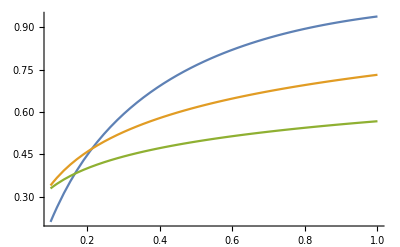

```mathematica
Plot[{th/.modifiedFrunkinIsotherm1mA[c],th/.modifiedFrunkinIsotherm2mA[c],th/.modifiedFrunkinIsotherm4mA[c]},{c,0.1,1}]
```

```mathematica
fit1mA = Table[{dat1mA[[n,1]],N[th/.modifiedFrunkinIsotherm1mANSolve[dat1mA[[n,2]]]]},{n,1,Length[dat1mA]}];
```

```mathematica
fit2mA = Table[{dat2mA[[n,1]],N[th/.modifiedFrunkinIsotherm2mANSolve[dat2mA[[n,2]]]]},{n,1,Length[dat2mA]}];
```

```mathematica
fit4mA = Table[{dat4mA[[n,1]],N[th/.modifiedFrunkinIsotherm4mANSolve[dat4mA[[n,2]]]]},{n,1,Length[dat4mA]}];
```

```mathematica
massPrediction1mA = Table[{dat1mA[[n,1]],
N[th/.modifiedFrunkinIsotherm1mANSolve[dat1mA[[n,2]]]]
*(Last[refReverseLogIsotherm1mA][[1]]-First[refReverseLogIsotherm1mA][[1]])+First[refReverseLogIsotherm1mA][[1]]},{n,1,Length[dat1mA]}];
```

```mathematica
massPrediction2mA = Table[{dat2mA[[n,1]],
N[th/.modifiedFrunkinIsotherm2mANSolve[dat2mA[[n,2]]]]
*(Last[refReverseLogIsotherm2mA][[1]]-First[refReverseLogIsotherm2mA][[1]])+First[refReverseLogIsotherm2mA][[1]]},{n,1,Length[dat2mA]}];
```

```mathematica
massPrediction4mA = Table[{dat4mA[[n,1]],
N[th/.modifiedFrunkinIsotherm4mANSolve[dat4mA[[n,2]]]]
*(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])+First[refReverseLogIsotherm4mA][[1]]},{n,1,Length[dat4mA]}];
```

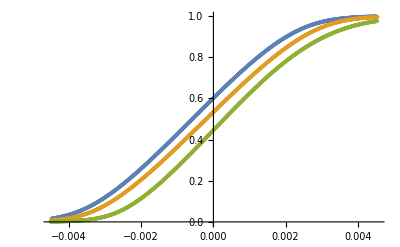

```mathematica
ListPlot[{fit1mA,fit2mA,fit4mA}]
```

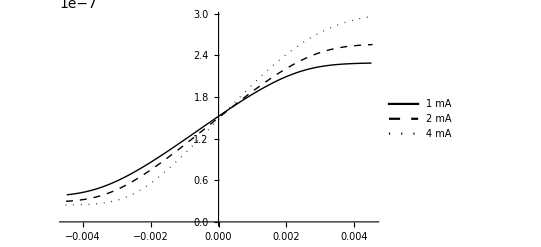

```mathematica
massPredictionPlot=ListLinePlot[{massPrediction1mA,massPrediction2mA,massPrediction4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[{"1 mA","2 mA","4 mA"},{0.75,0.25}]]
```

```mathematica
Show
```

Show

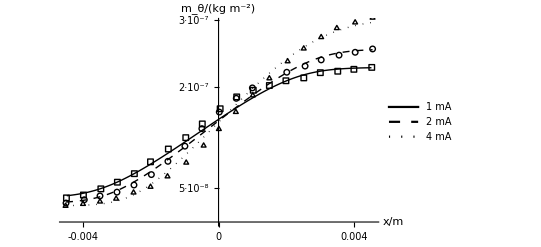

```mathematica
Show[massPredictionPlot,trueMassPlot,AxesLabel->{Text[x]/Text[m],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
Ticks->{{-0.004,0,0.004},
{{5.0*^-8,Text[5]·Text[10]^Text[-8]},
{1.0*^-7, ""},{1.5*^-7, ""},
{2.0*^-7,Text[2]·Text[10]^Text[-7]},
{2.5*^-7,""},
{3.0*^-7,Text[3]·Text[10]^Text[-7]}}}]
```

```mathematica
lineStyles={Directive[Black,Thick],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]}
```

{Directive[-Graphics-,Thickness[Large]],Directive[-Graphics-,Thickness[Large],Dashing[{Small,Small}]],Directive[-Graphics-,Thickness[Large],Dashing[{0,Small}]]}

```mathematica
lineStyles={Directive[Black,Thick],Directive[Black,Thick],Directive[Black,Thick]}
```

{Directive[GrayLevel[0],Thickness[Large]],Directive[GrayLevel[0],Thickness[Large]],Directive[GrayLevel[0],Thickness[Large]]}

```mathematica
{fm1,fm2,fm3}=Graphics/@{{EdgeForm[Thick],White,Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]},{EdgeForm[Thick],White,Disk[{0,0},1]},{EdgeForm[Thick],White,Polygon[{{-0.5,-0.5},{0.5,-0.5},{0,(Sqrt[3]-1)/2},{-0.5,-0.5}}]}}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
rasteredMarkers={Rasterize[fm1,RasterSize->15,ImageSize->15,Background->None],Rasterize[fm2,RasterSize->15,ImageSize->15],Rasterize[fm3,RasterSize->15,ImageSize->15]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
plegend2=PointLegend[Table[Black,{3}],{"","",""},LegendMarkerSize->{50,10},LegendMarkers->{{m1,1},{m2,1},{m3,1}},LabelStyle->{GrayLevel[0.0],12}]
```

```mathematica
llegend=LineLegend[lineStyles,{"1 mA","2 mA","4 mA"},LegendMarkerSize->{50,10},LabelStyle->{GrayLevel[0.0],12}]
```

```mathematica
plegendIndependent=PointLegend[Table[Black,{3}],{"1 mA, experimental","2 mA","4 mA"},LegendMarkerSize->{50,10},LegendMarkers->{{m1,1},{m2,1},{m3,1}},LabelStyle->{GrayLevel[0.0],12}]
```

```mathematica
llegendIndependent=LineLegend[lineStyles,{"1 mA, based on numerical results","2 mA","4 mA"},LegendMarkerSize->{50,10},LabelStyle->{GrayLevel[0.0],12}]
```

```mathematica
pllegend=LineLegend[lineStyles,{"1 mA","2 mA","4 mA"},LegendMarkerSize->{50,15},LegendMarkers->rasteredMarkers,LabelStyle->{GrayLevel[0.0],12}]
```

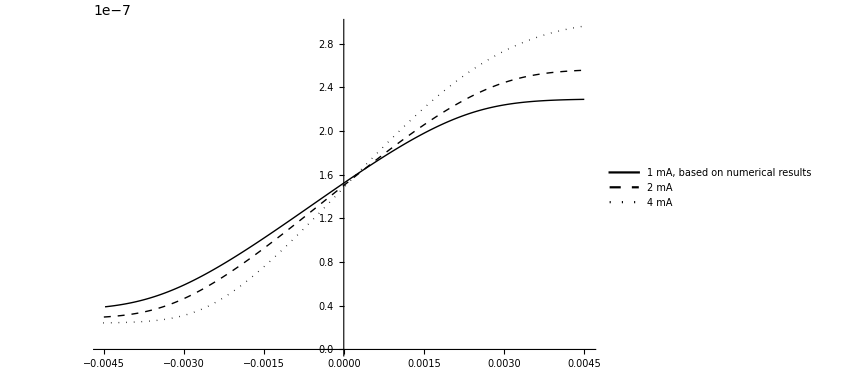

```mathematica
massPredictionPlotLineLegend=ListLinePlot[{massPrediction1mA,massPrediction2mA,massPrediction4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[llegendIndependent,{0.35,0.75}]]
```

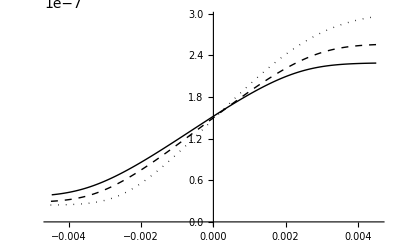

```mathematica
massPredictionPlotFullLegend=ListLinePlot[{massPrediction1mA,massPrediction2mA,massPrediction4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[pllegend,{0.75,0.25}]]
```

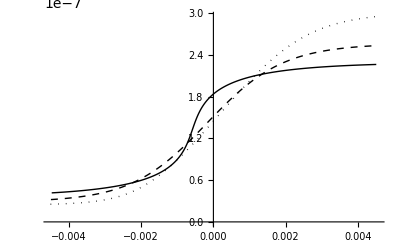

```mathematica
massPredictionDatPlotFullLegend=ListLinePlot[{massPredictionDat1mA,massPredictionDat2mA,massPredictionDat4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[pllegend,{0.75,0.25}]]
```

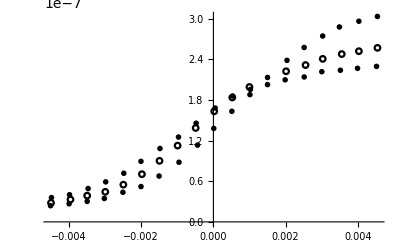

```mathematica
trueMassPlotMarkers=ListPlot[{adMass1mA,adMass2mA,adMass4mA},PlotStyle->Black,PlotMarkers->Table[{s,0.03},{s,{m1,m2,m3}}]]
```

```mathematica
trueMassPlotWithRawLegend=ListPlot[{adMass1mA,adMass2mA,adMass4mA},PlotStyle->Black,PlotMarkers->Table[{s,0.03},{s,{m1,m2,m3}}],PlotLegends->Placed[plegend2,{0.75,0.25}]]
```

-Graphics-

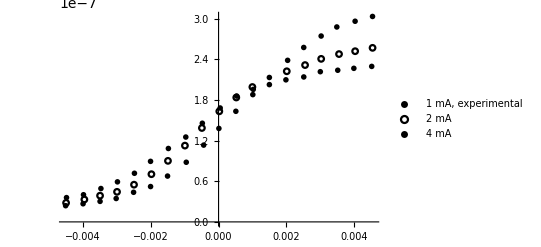

```mathematica
trueMassPlotPointLegend=ListPlot[{adMass1mA,adMass2mA,adMass4mA},PlotStyle->Black,PlotMarkers->Table[{s,0.03},{s,{m1,m2,m3}}],PlotLegends->Placed[plegendIndependent,{0.75,0.25}]]
```

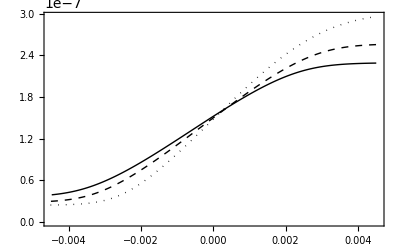

```mathematica
massPredictionPlotFramed=ListLinePlot[{massPrediction1mA,massPrediction2mA,massPrediction4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[pllegend,{0.75,0.25}],Frame->True,Axes->False]
```

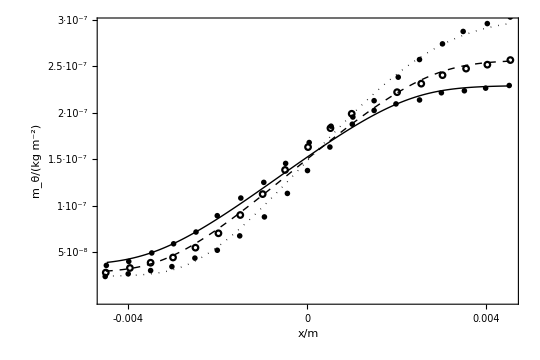

```mathematica
Show[massPredictionPlotFullLegend,trueMassPlotMarkers,FrameLabel->{Text[x]/Text[m],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
FrameTicks->{{{
{5.0*^-8,Text[5]·Text[10]^Text[-8]},
{1.0*^-7, Text[1]·Text[10]^Text[-7]},
{1.5*^-7, Text[1.5]·Text[10]^Text[-7]},
{2.0*^-7,Text[2]·Text[10]^Text[-7]},
{2.5*^-7,Text[2.5]·Text[10]^Text[-7]},
{3.0*^-7,Text[3]·Text[10]^Text[-7]}},None},{{-0.004,0,0.004},None}},Frame->True,Axes->False,AspectRatio->1/1.5]
```

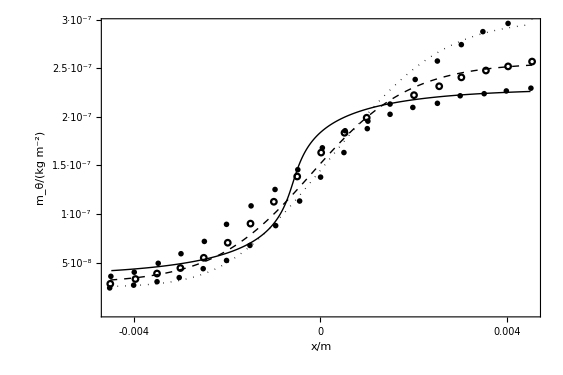

```mathematica
Show[massPredictionDatPlotFullLegend,trueMassPlotMarkers,FrameLabel->{Text[x]/Text[m],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
FrameTicks->{{{
{5.0*^-8,Text[5]·Text[10]^Text[-8]},
{1.0*^-7, Text[1]·Text[10]^Text[-7]},
{1.5*^-7, Text[1.5]·Text[10]^Text[-7]},
{2.0*^-7,Text[2]·Text[10]^Text[-7]},
{2.5*^-7,Text[2.5]·Text[10]^Text[-7]},
{3.0*^-7,Text[3]·Text[10]^Text[-7]}},None},{{-0.004,0,0.004},None}},Frame->True,Axes->False,AspectRatio->1/1.5]
```

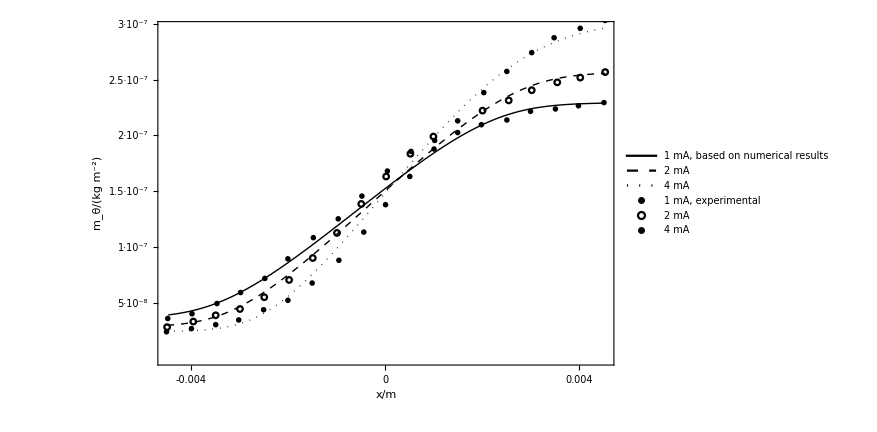

```mathematica
Show[massPredictionPlotLineLegend,trueMassPlotPointLegend,FrameLabel->{Text[x]/Text[m],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
FrameTicks->{{{
{5.0*^-8,Text[5]·Text[10]^Text[-8]},
{1.0*^-7, Text[1]·Text[10]^Text[-7]},
{1.5*^-7, Text[1.5]·Text[10]^Text[-7]},
{2.0*^-7,Text[2]·Text[10]^Text[-7]},
{2.5*^-7,Text[2.5]·Text[10]^Text[-7]},
{3.0*^-7,Text[3]·Text[10]^Text[-7]}},None},{{-0.004,0,0.004},None}},Frame->True,Axes->False,AspectRatio->1/1.5]
```

```mathematica
N[Quantity[None,"FaradayConstant"]*Quantity[None,"MolarGasConstant"]]
```

1. F R

```mathematica
DumpSave["frumkin.mx",{}]
```

## Comparison to zhang2014stick

```mathematica
zhang2014stickFig2dat=Import["fig2_sds_isotherm.txt","CSV"];
```

```mathematica
zhang2014stickFig2dat
```

{{0.0101658,2.7834},{0.0196665,4.65951},{0.0489411,8.8803},{0.0992772,11.9423},{0.198481,19.3852},{0.502337,27.9815},{1.00323,31.4442},{2.00464,36.8971},{2.98055,52.3519},{3.96994,67.4277},{5.04883,85.6957},{6.12618,104.37},{7.19595,119.069},{8.16239,120.64},{12.2833,122.559},{15.5513,124.111},{20.6384,125.654}}

```mathematica
zhang2014stickFig4dat=Import["fig4_friction_coefficient.txt","CSV"]
```

{{0.01,0.419704},{0.0201279,0.366502},{0.0489636,0.248276},{0.1,0.107882},{0.198367,0.0886699},{0.307144,0.0886699},{0.489636,0.0871921},{0.985532,0.0871921},{2.01279,0.0886699},{4.96824,0.0886699},{7.92016,0.0886699},{12.0859,0.0901478},{15.0389,0.0886699},{20.1279,0.0886699}}

```mathematica
zhang2014stickFig2dat[[1,2]]
```

2.7834

```mathematica
zhang2014stickFig2datNormalized=Table[{zhang2014stickFig2dat[[n]][[1]],zhang2014stickFig2dat[[n]][[2]]/10^12*100^2},{n,1,Length[zhang2014stickFig2dat]}];
```

```mathematica
c1mA=Table[{dat1mA[[n]][[1]],dat1mA[[n]][[2]]},{n,1,Length[dat1mA]}];
```

```mathematica
c2mA=Table[{dat2mA[[n]][[1]],dat2mA[[n]][[2]]},{n,1,Length[dat2mA]}];
```

```mathematica
c4mA=Table[{dat4mA[[n]][[1]],dat4mA[[n]][[2]]},{n,1,Length[dat4mA]}];
```

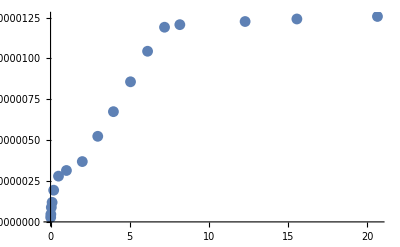

```mathematica
ListPlot[zhang2014stickFig2datNormalized]
```

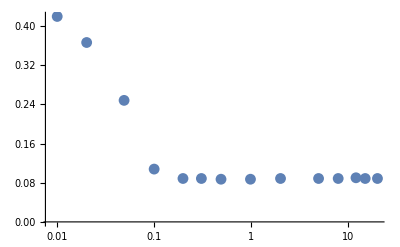

```mathematica
ListLogLinearPlot[zhang2014stickFig4dat]
```

```mathematica
zhang2014stickFig2datNormalizedInterpolation=Interpolation[zhang2014stickFig2datNormalized,InterpolationOrder->1]
```

InterpolatingFunction[{{0.0101658, 20.6384}}, <>]

```mathematica
zhang2014stickFig2datNormalizedInterpolation2ndOrder=Interpolation[zhang2014stickFig2datNormalized,InterpolationOrder->2]
```

InterpolatingFunction[{{0.0101658, 20.6384}}, <>]

```mathematica
zhang2014stickFig2datNormalizedInterpolationSpline1stOrder=Interpolation[zhang2014stickFig2datNormalized,Method->"Spline",InterpolationOrder->1]
```

InterpolatingFunction[{{0.0101658, 20.6384}}, <>]

```mathematica
zhang2014stickFig2datNormalizedInterpolationSpline2ndOrder=Interpolation[zhang2014stickFig2datNormalized,Method->"Spline",InterpolationOrder->2]
```

InterpolatingFunction[{{0.0101658, 20.6384}}, <>]

```mathematica
zhang2014stickFig4datInterpolation=Interpolation[zhang2014stickFig4dat,InterpolationOrder->1]
```

InterpolatingFunction[{{0.01, 20.1279}}, <>]

```mathematica
zhang2014stickFig4datInterpolationSpline1stOrder=Interpolation[zhang2014stickFig4dat,InterpolationOrder->1,Method->"Spline"]
```

InterpolatingFunction[{{0.01, 20.1279}}, <>]

```mathematica
zhang2014stickFig4datInterpolation2ndOrder=Interpolation[zhang2014stickFig4dat,InterpolationOrder->2]
```

InterpolatingFunction[{{0.01, 20.1279}}, <>]

```mathematica
zhang2014stickFig4datInterpolation3rdOrder=Interpolation[zhang2014stickFig4dat,InterpolationOrder->13]
```

InterpolatingFunction[{{0.01, 20.1279}}, <>]

```mathematica
zhang2014stickFig4datInterpolationSpline2ndOrder=Interpolation[zhang2014stickFig4dat,Method->"Spline",InterpolationOrder->2]
```

```mathematica
zhang2014stickFig4datInterpolatingPolynomial=.
```

```mathematica
zhang2014stickFig4datInterpolatingPolynomial[x_]:=Evaluate[InterpolatingPolynomial[zhang2014stickFig4dat,c]]/.c->x
```

```mathematica
zhang2014stickFig4datInterpolatingPolynomial[1]
```

-11.7998

InterpolatingFunction::dmval: Input value {0.000306429} lies outside the range of data in the interpolating function. Extrapolation will be used.

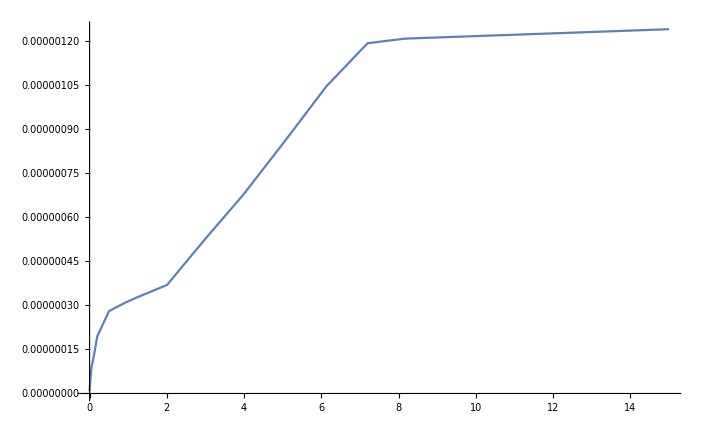

```mathematica
Plot[zhang2014stickFig2datNormalizedInterpolation[x],{x,0,15}]
```

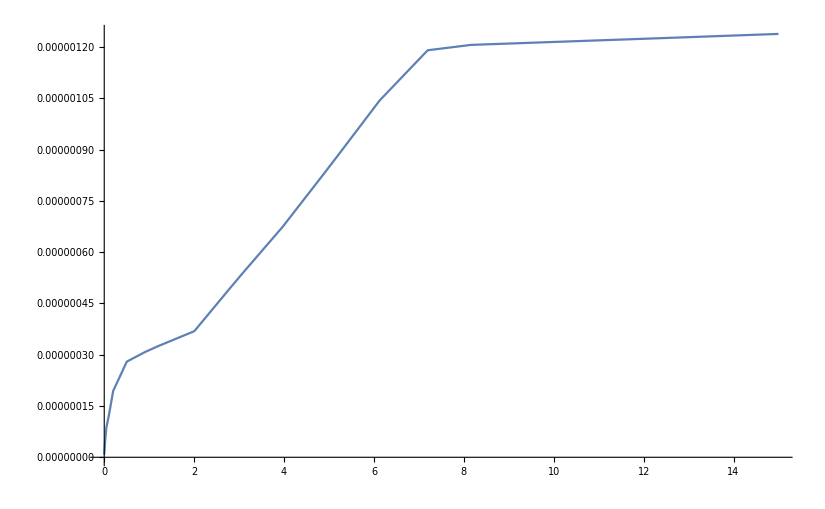

```mathematica
Plot[zhang2014stickFig2datNormalizedInterpolationSpline1stOrder[x],{x,0,15}]
```

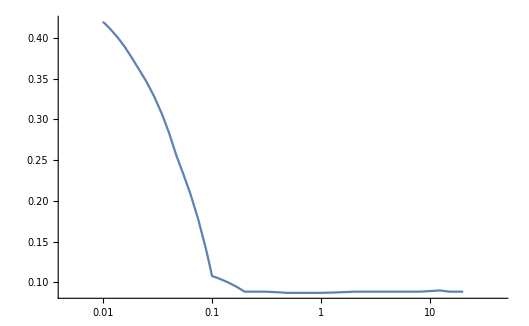

```mathematica
LogLinearPlot[zhang2014stickFig4datInterpolation[x],{x,0.01,20}]
```

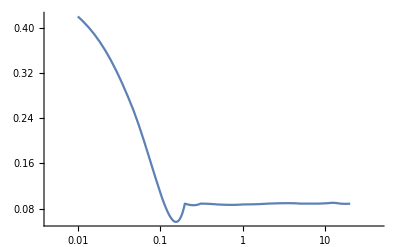

```mathematica
LogLinearPlot[zhang2014stickFig4datInterpolation2ndOrder[x],{x,0.01,20}]
```

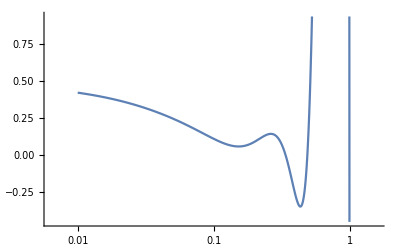

```mathematica
LogLinearPlot[zhang2014stickFig4datInterpolatingPolynomial[x],{x,0.01,1}]
```

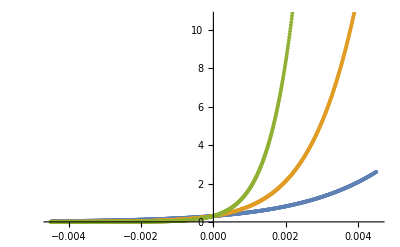

```mathematica
ListPlot[{c1mA,c2mA,c4mA}]
```

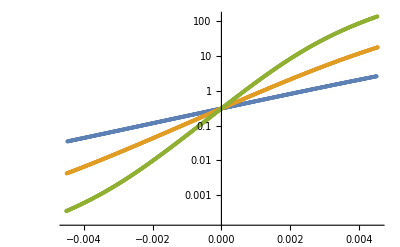

```mathematica
ListLogPlot[{c1mA,c2mA,c4mA}]
```

```mathematica
Length[c2mA]
```

823

```mathematica
c2mA[[823]]
```

{0.004543,17.7685}

```mathematica
zhang2014stickFig2datNormalizedInterpolation[c2mA[[823]][[2]]]
```

0.00124784

```mathematica
predictedAdsorption1mA=Table[{c1mA[[n]][[1]],zhang2014stickFig2datNormalizedInterpolationSpline1stOrder[c1mA[[n]][[2]]]},{n,1,Length[c1mA]}];
```

```mathematica
predictedAdsorption2mA=Table[{c2mA[[n]][[1]],zhang2014stickFig2datNormalizedInterpolationSpline1stOrder[c2mA[[n]][[2]]]},{n,1,Length[c2mA]}];
```

```mathematica
predictedAdsorption4mA=Table[{c4mA[[n]][[1]],zhang2014stickFig2datNormalizedInterpolationSpline1stOrder[c4mA[[n]][[2]]]},{n,1,Length[c4mA]}];
```

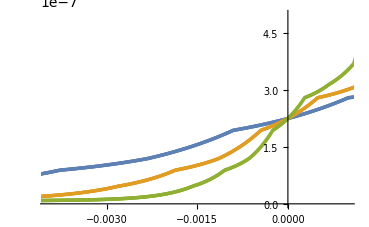

```mathematica
ListPlot[{predictedAdsorption1mA,predictedAdsorption2mA,predictedAdsorption4mA},PlotRange->{{-0.004,0.001},{0,5*10^-7}}]
```

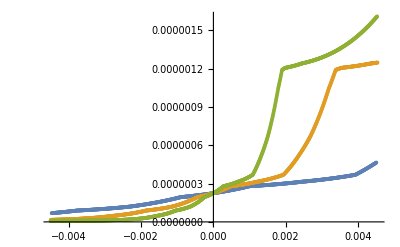

```mathematica
ListPlot[{predictedAdsorption1mA,predictedAdsorption2mA,predictedAdsorption4mA}]
```

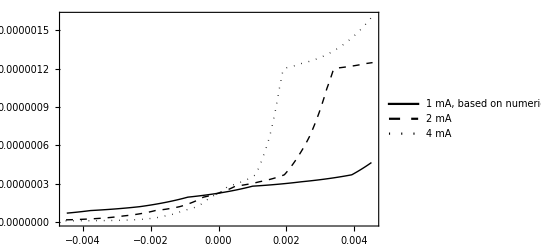

```mathematica
predictedAdsorptionMassPlotFramed=ListLinePlot[{predictedAdsorption1mA,predictedAdsorption2mA,predictedAdsorption4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[llegendIndependent,{0.35,0.75}],Frame->True,Axes->False]
```

```mathematica
Export["zhang2015control_adsorbed_mass_comparison_0_0011A.png",Show[predictedAdsorptionMassPlotFramed,trueMassPlotPointLegend,FrameLabel->{Text[x]/Text[m],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
FrameTicks->{{{
{5.0*^-8,Text[5.0]·Text[10]^Text[-8]},
{1.0*^-7, Text[1.0]·Text[10]^Text[-7]},
{1.5*^-7, Text[1.5]·Text[10]^Text[-7]},
{2.0*^-7,Text[2.0]·Text[10]^Text[-7]},
{2.5*^-7,Text[2.5]·Text[10]^Text[-7]},
{3.0*^-7,Text[3.0]·Text[10]^Text[-7]},
{3.5*^-7,Text[3.5]·Text[10]^Text[-7]},
{4.0*^-7,Text[4.0]·Text[10]^Text[-7]}},None},{{-0.005,-0.0025,0,0.0025,0.005},None}},
Frame->True,
Axes->False,
AspectRatio->1/1.5,
PlotRange->{{-0.005,0.005},{0,4*10^-7}},
ImageSize->{2.51*300,Automatic}],
ImageResolution->300]
```

zhang2015control_adsorbed_mass_comparison_0_0011A.png

```mathematica
Export["zhang2015control_adsorbed_mass_comparison_0_0011A.pdf",Show[predictedAdsorptionMassPlotFramed,trueMassPlotPointLegend,FrameLabel->{Text[x]/Text[m],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
FrameTicks->{{{
{5.0*^-8,Text[5.0]·Text[10]^Text[-8]},
{1.0*^-7, Text[1.0]·Text[10]^Text[-7]},
{1.5*^-7, Text[1.5]·Text[10]^Text[-7]},
{2.0*^-7,Text[2.0]·Text[10]^Text[-7]},
{2.5*^-7,Text[2.5]·Text[10]^Text[-7]},
{3.0*^-7,Text[3.0]·Text[10]^Text[-7]},
{3.5*^-7,Text[3.5]·Text[10]^Text[-7]},
{4.0*^-7,Text[4.0]·Text[10]^Text[-7]}},None},{{-0.005,-0.0025,0,0.0025,0.005},None}},
Frame->True,
Axes->False,
AspectRatio->1/1.5,
PlotRange->{{-0.005,0.005},{0,4*10^-7}},
ImageSize->{2.51*300,Automatic}],
ImageResolution->300]
```

zhang2015control_adsorbed_mass_comparison_0_0011A.pdf

```mathematica
predictedFrictionCoefficient1mA=Table[{c1mA[[n]][[1]],zhang2014stickFig4datInterpolation[c1mA[[n]][[2]]]},{n,1,Length[c1mA]}];
```

```mathematica
predictedFrictionCoefficient2mA=Table[{c2mA[[n]][[1]],zhang2014stickFig4datInterpolation[c2mA[[n]][[2]]]},{n,1,Length[c2mA]}];
```

InterpolatingFunction::dmval: Input value {0.00418984} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00422965} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00426988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
predictedFrictionCoefficient4mA=Table[{c4mA[[n]][[1]],zhang2014stickFig4datInterpolation[c4mA[[n]][[2]]]},{n,1,Length[c4mA]}];
```

InterpolatingFunction::dmval: Input value {0.000346455} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00035023} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000354058} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

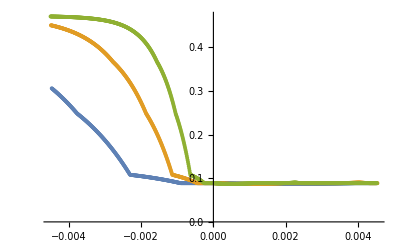

```mathematica
ListPlot[{predictedFrictionCoefficient1mA,predictedFrictionCoefficient2mA,predictedFrictionCoefficient4mA}]
```

```mathematica
100^2/10^6
```

1/100

```mathematica
80/100
```

4/5

```mathematica
mu1mA=Import["zhang2015control_friction_coefficient_fig5_0_1mA.txt","Table"];
```

```mathematica
mu2mA=Import["zhang2015control_friction_coefficient_fig5_0_2mA.txt","Table"];
```

```mathematica
mu4mA=Import["zhang2015control_friction_coefficient_fig5_0_4mA.txt","Table"];
```

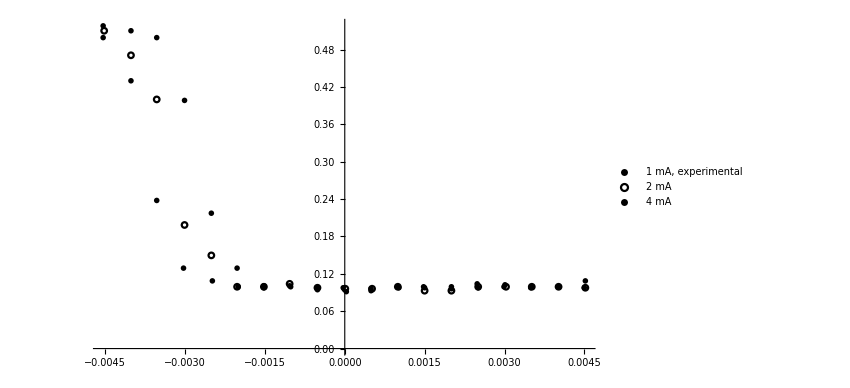

```mathematica
muPlotWithLegend=ListPlot[{mu1mA,mu2mA,mu4mA},PlotStyle->Black,PlotMarkers->Table[{s,0.03},{s,{m1,m2,m3}}],PlotLegends->Placed[plegendIndependent,{0.7,0.5}]]
```

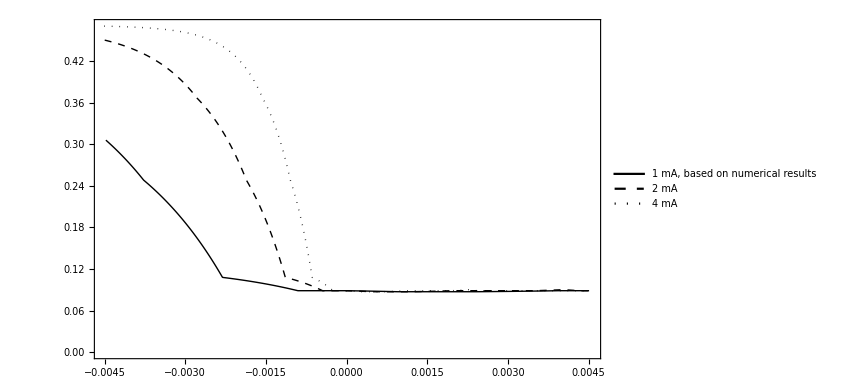

```mathematica
muPredictionPlotFramed=ListLinePlot[{predictedFrictionCoefficient1mA,predictedFrictionCoefficient2mA,predictedFrictionCoefficient4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[llegendIndependent,{0.75,0.75}],Frame->True,Axes->False]
```

```mathematica
Export["zhang2015control_friction_coefficient_comparison_0_0011A.png",Show[muPlotWithLegend,muPredictionPlotFramed,FrameLabel->{Text[x]/Text[m],Text[μ]},
LabelStyle->Directive[Black],
FrameTicks->{{{
0,0.1,0.2,0.3,0.4,0.5},None},{{-0.005,-0.0025,0,0.0025,0.005},None}},Frame->True,Axes->False,AspectRatio->1/1.5,
PlotRange->{{-0.005,0.005},{0,0.6}},
ImageSize->{2.52*300,Automatic}],
ImageResolution->300]
```

zhang2015control_friction_coefficient_comparison_0_0011A.png

```mathematica
Export["zhang2015control_friction_coefficient_comparison_0_0011A.pdf",Show[muPlotWithLegend,muPredictionPlotFramed,FrameLabel->{Text[x]/Text[m],Text[μ]},
LabelStyle->Directive[Black],
FrameTicks->{{{
0,0.1,0.2,0.3,0.4,0.5},None},{{-0.005,-0.0025,0,0.0025,0.005},None}},Frame->True,Axes->False,AspectRatio->1/1.5,
PlotRange->{{-0.005,0.005},{0,0.6}},
ImageSize->{2.52*300,Automatic}],
ImageResolution->300]
```

zhang2015control_friction_coefficient_comparison_0_0011A.pdf

## Results for 1 A / m^2 current density

```mathematica
surfaceData1mA=Import["zhang2015control_pde1d_global_0_1563V.txt","Table"];
```

```mathematica
surfaceData1mA[[1]]
```

{X,intSurface(Ix),intSurface(NClO4m),intSurface(NClO4mx),intSurface(NDSm),intSurface(NDSmx),intSurface(NH3Op),intSurface(NH3Opx),intSurface(NNap),intSurface(NNapx),intSurface(NOHm),intSurface(NOHmx),intSurface(cH3Op),intSurface(cOHm),intSurface(cDSm),intSurface(cNap),intSurface(cClO4m),intSurface(cH3Opx),intSurface(cOHmx),intSurface(cDSmx),intSurface(cNapx),intSurface(cClO4mx),intSurface(phi),intSurface(phix),intSurface(log(cH3Op)),intSurface(log(cOHm)),intSurface(log(cDSm)),intSurface(log(cNap)),intSurface(log(cClO4m)),intSurface(-DH3Op*cH3Opx),intSurface(-DOHm*cOHmx),intSurface(-DDSm*cDSmx),intSurface(-DNap*cNapx),intSurface(-DClO4m*cClO4mx),intSurface(-zH3Op*DH3Op*cH3Op*F_const/RT*phix),intSurface(-zOHm*DOHm*cOHm*F_const/RT*phix),intSurface(-zDSm*DDSm*cDSm*F_const/RT*phix),intSurface(-zNap*DNap*cNap*F_const/RT*phix),intSurface(-zClO4m*DClO4m*cClO4m*F_const/RT*phix),intSurface(i_AnodicWaterDissotiation),intSurface(i_CathodicWaterDissotiation),intSurface(i_anodic),intSurface(i_cathodic),intSurface(i_total),log(abs(intSurface(i_cathodic))),log(abs(intSurface(i_anodic))),log(abs(intSurface(i_anodic))),log(abs(intSurface(i_cathodic))),intSurface(-DH3Op*cH3Opx)+intSurface(-zH3Op*DH3Op*cH3Op*F_const/RT*phix),intSurface(-DOHm*cOHmx)+intSurface(-zOHm*DOHm*cOHm*F_const/RT*phix),intSurface(-DDSm*cDSmx)+intSurface(-zDSm*DDSm*cDSm*F_const/RT*phix),intSurface(-DNap*cNapx)+intSurface(-zNap*DNap*cNap*F_const/RT*phix),intSurface(-DClO4m*cClO4mx)+intSurface(-zClO4m*DClO4m*cClO4m*F_const/RT*phix)}

```mathematica
surfaceConcentration1mA=Table[{surfaceData1mA[[n]][[1]],surfaceData1mA[[n]][[15]]},{n,2,Length[surfaceData1mA]}];
```

```mathematica
surfaceData2mA=Import["zhang2015control_pde1d_global_0_3166V.txt","Table"];
```

```mathematica
surfaceConcentration2mA=Table[{surfaceData2mA[[n]][[1]],surfaceData2mA[[n]][[15]]},{n,2,Length[surfaceData2mA]}];
```

```mathematica
surfaceData4mA=Import["zhang2015control_pde1d_global_0_5641V.txt","Table"];
```

```mathematica
surfaceConcentration4mA=Table[{surfaceData4mA[[n]][[1]],surfaceData4mA[[n]][[15]]},{n,2,Length[surfaceData4mA]}];
```

```mathematica
predictedAdsorption1mAat1A=Table[{surfaceConcentration1mA[[n]][[1]],zhang2014stickFig2datNormalizedInterpolationSpline2ndOrder[surfaceConcentration1mA[[n]][[2]]]},{n,1,Length[surfaceConcentration1mA]}];
```

```mathematica
predictedAdsorption2mAat1A=Table[{surfaceConcentration2mA[[n]][[1]],zhang2014stickFig2datNormalizedInterpolationSpline2ndOrder[surfaceConcentration2mA[[n]][[2]]]},{n,1,Length[surfaceConcentration2mA]}];
```

```mathematica
predictedAdsorption4mAat1A=Table[{surfaceConcentration4mA[[n]][[1]],zhang2014stickFig2datNormalizedInterpolationSpline2ndOrder[surfaceConcentration4mA[[n]][[2]]]},{n,1,Length[surfaceConcentration4mA]}];
```

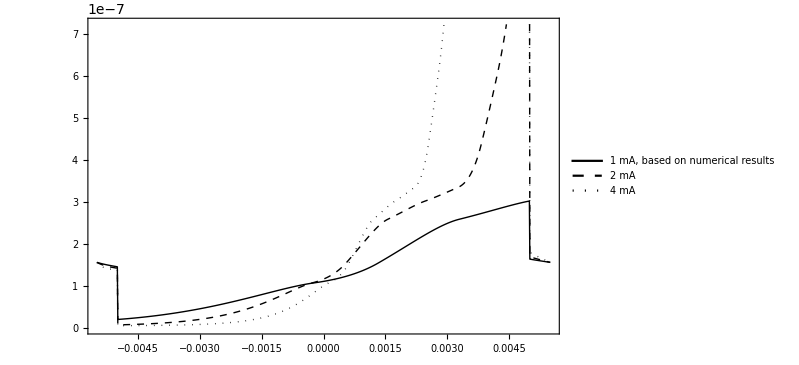

```mathematica
predictedAdsorptionMassAt1APlotFramed=ListLinePlot[{predictedAdsorption1mAat1A,predictedAdsorption2mAat1A,predictedAdsorption4mAat1A},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[llegendIndependent,{0.35,0.75}],Frame->True,Axes->False]
```

```mathematica
Export["zhang2015control_adsorbed_mass_comparison_1A.png",Show[predictedAdsorptionMassAt1APlotFramed,trueMassPlotPointLegend,FrameLabel->{Text[x]/Text[m],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
FrameTicks->{{{
{5.0*^-8,Text[5.0]·Text[10]^Text[-8]},
{1.0*^-7, Text[1.0]·Text[10]^Text[-7]},
{1.5*^-7, Text[1.5]·Text[10]^Text[-7]},
{2.0*^-7,Text[2.0]·Text[10]^Text[-7]},
{2.5*^-7,Text[2.5]·Text[10]^Text[-7]},
{3.0*^-7,Text[3.0]·Text[10]^Text[-7]},
{3.5*^-7,Text[3.5]·Text[10]^Text[-7]},
{4.0*^-7,Text[4.0]·Text[10]^Text[-7]}},None},{{-0.005,-0.0025,0,0.0025,0.005},None}},
Frame->True,
Axes->False,
AspectRatio->1/1.5,
PlotRange->{{-0.005,0.005},{0,4*10^-7}},
ImageSize->{2.51*300,Automatic}],
ImageResolution->300]
```

zhang2015control_adsorbed_mass_comparison_1A.png

```mathematica
Export["zhang2015control_adsorbed_mass_comparison_1A.pdf",Show[predictedAdsorptionMassAt1APlotFramed,trueMassPlotPointLegend,FrameLabel->{Text[x]/Text[m],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
FrameTicks->{{{
{5.0*^-8,Text[5.0]·Text[10]^Text[-8]},
{1.0*^-7, Text[1.0]·Text[10]^Text[-7]},
{1.5*^-7, Text[1.5]·Text[10]^Text[-7]},
{2.0*^-7,Text[2.0]·Text[10]^Text[-7]},
{2.5*^-7,Text[2.5]·Text[10]^Text[-7]},
{3.0*^-7,Text[3.0]·Text[10]^Text[-7]},
{3.5*^-7,Text[3.5]·Text[10]^Text[-7]},
{4.0*^-7,Text[4.0]·Text[10]^Text[-7]}},None},{{-0.005,-0.0025,0,0.0025,0.005},None}},
Frame->True,
Axes->False,
AspectRatio->1/1.5,
PlotRange->{{-0.005,0.005},{0,4*10^-7}},
ImageSize->{2.51*300,Automatic}],
ImageResolution->300]
```

zhang2015control_adsorbed_mass_comparison_1A.pdf

```mathematica
predictedFrictionCoefficient1mAat1A=Table[{surfaceConcentration1mA[[n]][[1]],zhang2014stickFig4datInterpolationSpline1stOrder[surfaceConcentration1mA[[n]][[2]]]},{n,1,Length[surfaceConcentration1mA]}];
```

```mathematica
predictedFrictionCoefficient2mAat1A=Table[{surfaceConcentration2mA[[n]][[1]],zhang2014stickFig4datInterpolationSpline1stOrder[surfaceConcentration2mA[[n]][[2]]]},{n,1,Length[surfaceConcentration2mA]}];
```

```mathematica
predictedFrictionCoefficient4mAat1A=Table[{surfaceConcentration4mA[[n]][[1]],zhang2014stickFig4datInterpolationSpline1stOrder[surfaceConcentration4mA[[n]][[2]]]},{n,1,Length[surfaceConcentration4mA]}];
```

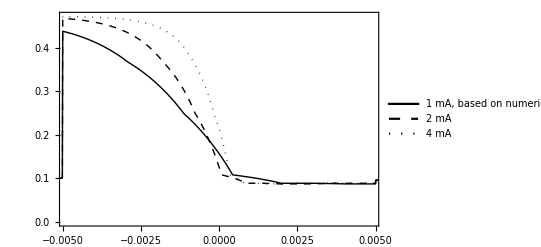

```mathematica
muPredictionAt1APlotFramed=ListLinePlot[{predictedFrictionCoefficient1mAat1A,predictedFrictionCoefficient2mAat1A,predictedFrictionCoefficient4mAat1A},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[llegendIndependent,{0.75,0.75}],Frame->True,Axes->False,
DataRange->{-0.0049,0.0049},PlotRange->{{-0.0049,0.0049},Automatic},PlotRangeClipping->True]
```

```mathematica
Export["zhang2015control_friction_coefficient_comparison_1A.png",Show[muPlotWithLegend,muPredictionAt1APlotFramed,FrameLabel->{Text[x]/Text[m],Text[μ]},
LabelStyle->Directive[Black],
FrameTicks->{{{
0,0.1,0.2,0.3,0.4,0.5},None},{{-0.005,-0.0025,0,0.0025,0.005},None}},Frame->True,Axes->False,AspectRatio->1/1.5,
PlotRange->{{-0.005,0.005},{0,0.6}},PlotRangeClipping->True,
ImageSize->{2.52*300,Automatic}],
ImageResolution->300]
```

zhang2015control_friction_coefficient_comparison_1A.png

```mathematica
Export["zhang2015control_friction_coefficient_comparison_1A.pdf",Show[muPlotWithLegend,muPredictionAt1APlotFramed,FrameLabel->{Text[x]/Text[m],Text[μ]},
LabelStyle->Directive[Black],
FrameTicks->{{{
0,0.1,0.2,0.3,0.4,0.5},None},{{-0.005,-0.0025,0,0.0025,0.005},None}},Frame->True,Axes->False,AspectRatio->1/1.5,
PlotRange->{{-0.005,0.005},{0,0.6}},PlotRangeClipping->True,
ImageSize->{2.52*300,Automatic}],
ImageResolution->300]
```

zhang2015control_friction_coefficient_comparison_1A.pdf

## Isotherm Comparison

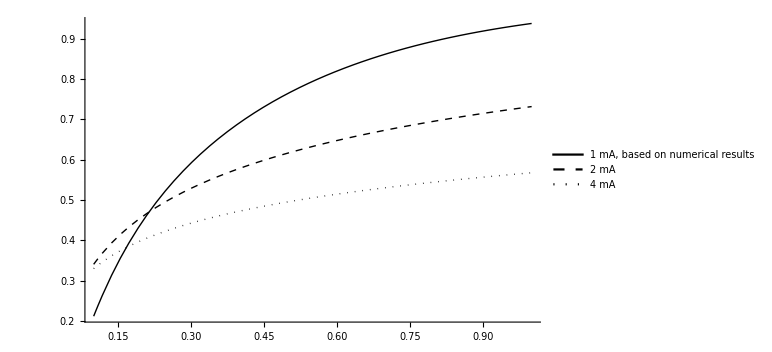

```mathematica
cThIsothermPlot=Plot[{th/.modifiedFrunkinIsotherm1mA[c],th/.modifiedFrunkinIsotherm2mA[c],th/.modifiedFrunkinIsotherm4mA[c]},{c,0.1,1},
PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[llegendIndependent,{0.25,0.75}]]
```

```mathematica
cmIsothermPrediction1mA = Table[{dat1mA[[n,2]],
N[th/.modifiedFrunkinIsotherm1mANSolve[dat1mA[[n,2]]]]
*(Last[refReverseLogIsotherm1mA][[1]]-First[refReverseLogIsotherm1mA][[1]])+First[refReverseLogIsotherm1mA][[1]]},{n,1,Length[dat1mA]}];
```

```mathematica
cmIsothermPrediction2mA = Table[{dat2mA[[n,2]],
N[th/.modifiedFrunkinIsotherm2mANSolve[dat2mA[[n,2]]]]
*(Last[refReverseLogIsotherm2mA][[1]]-First[refReverseLogIsotherm2mA][[1]])+First[refReverseLogIsotherm2mA][[1]]},{n,1,Length[dat2mA]}];
```

```mathematica
cmIsothermPrediction4mA = Table[{dat4mA[[n,2]],
N[th/.modifiedFrunkinIsotherm4mANSolve[dat4mA[[n,2]]]]
*(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])+First[refReverseLogIsotherm4mA][[1]]},{n,1,Length[dat4mA]}];
```

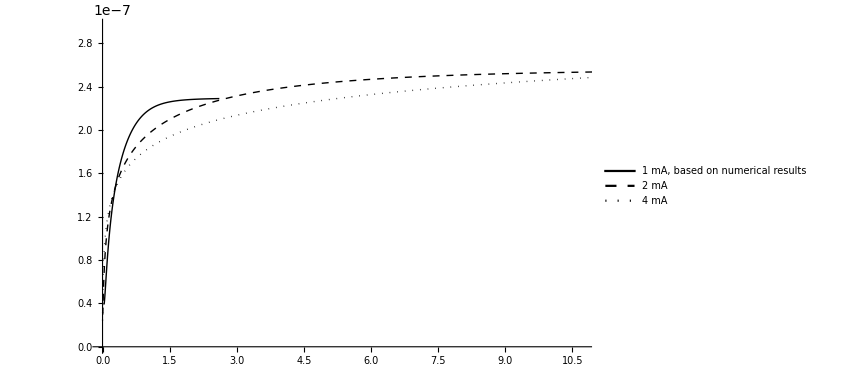

```mathematica
numericalCmIsothermPlot=ListLinePlot[{cmIsothermPrediction1mA,cmIsothermPrediction2mA,cmIsothermPrediction4mA},
PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[llegendIndependent,{0.7,0.3}]]
```

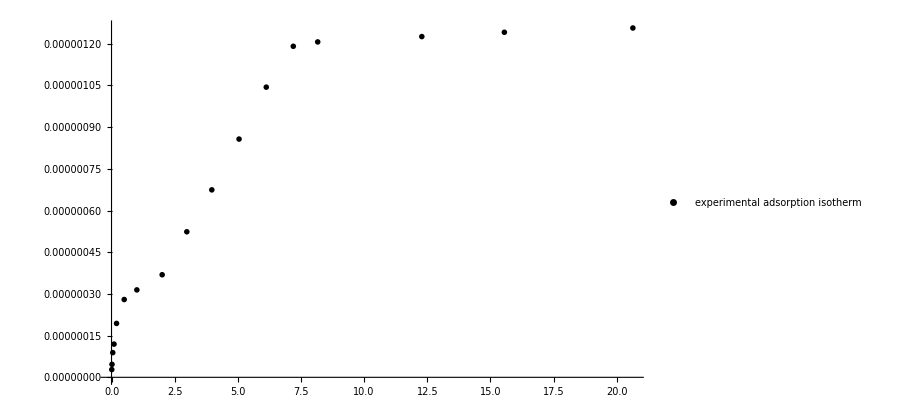

```mathematica
experimentalCmIsothermPlot=ListPlot[zhang2014stickFig2datNormalized,PlotStyle->Black,PlotMarkers->{m1,0.02},PlotLegends->Placed[PointLegend[{"experimental adsorption isotherm"},LegendMarkers->m1],{0.7,0.5}]]
```

```mathematica
Export["zhang2015control_concentration_mass_isotherm_comparison.png",Show[numericalCmIsothermPlot,experimentalCmIsothermPlot,FrameLabel->{Text[c]/Text["mol m"^"-3"],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
FrameTicks->{{{
{2*^-7,Text[2]·Text[10]^Text[-7]},
{4*^-7,Text[4]·Text[10]^Text[-7]},
{6*^-7,Text[6]·Text[10]^Text[-7]},
{8*^-7,Text[8]·Text[10]^Text[-7]},
{1*^-6,Text[1]·Text[10]^Text[-6]}},None},{Automatic,None}},
Frame->True,
Axes->False,
AspectRatio->1/1.5,
PlotRange->{{0,20},{0,1.2*10^-6}},
ImageSize->{2.51*300,Automatic}],
ImageResolution->300]
```

zhang2015control_concentration_mass_isotherm_comparison.png

```mathematica
Export["zhang2015control_concentration_mass_isotherm_comparison.pdf",Show[numericalCmIsothermPlot,experimentalCmIsothermPlot,FrameLabel->{Text[c]/Text["mol m"^"-3"],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
FrameTicks->{{{
{2*^-7,Text[2]·Text[10]^Text[-7]},
{4*^-7,Text[4]·Text[10]^Text[-7]},
{6*^-7,Text[6]·Text[10]^Text[-7]},
{8*^-7,Text[8]·Text[10]^Text[-7]},
{1*^-6,Text[1]·Text[10]^Text[-6]}},None},{Automatic,None}},
Frame->True,
Axes->False,
AspectRatio->1/1.5,
PlotRange->{{0,20},{0,1.2*10^-6}},
ImageSize->{2.51*300,Automatic}],
ImageResolution->300]
```

zhang2015control_concentration_mass_isotherm_comparison.pdf

```mathematica
DumpSave["empiricalIsotherm.mx","Global`"]
```

{Global`}